```mathematica
Ising:
```

```mathematica
LogmaxdabsMdk
LogvabsmpmaxdabsMdk
pmaxdabsMdk
pmaxdabsMdk1
```

{{Log[16],3.80877},{Log[24],4.26654},{Log[32],4.58888},{Log[48],5.04109},{Log[64],5.33889}}

{{Log[16],-1.11263},{Log[24],-1.3021},{Log[32],-1.43688},{Log[48],-1.64649},{Log[64],-1.80375}}

{{16,0.22313},{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

{{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

```mathematica
ν=1/1.6051220837004385;
k0=0.221671;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[LogvabsmpmaxdabsMdk,model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdabsMdk1,model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdabsMdk1,model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdabsMdk1,model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^1.60512

0.221671+c0 x^-ex0

{0.276744-0.497841 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.276744 | 0.0345842 | 8.00204 | 0.00407358
b0 | 0.497841 | 0.00981484 | 50.7233 | 0.0000168749}

{0.221545+0.0458316/x^1.2212, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221545 | 8.41127×10^-7 | 263390. | 2.41702×10^-6
c0 | 0.0458316 | 0.000238353 | 192.284 | 0.0033108
ex0 | 1.2212 | 0.00189262 | 645.244 | 0.000986633}

{0.221671+0.136026/x^1.60512, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221671 | 0.0000172826 | 12826.3 | 6.07851×10^-9
c0 | 0.136026 | 0.00456195 | 29.8175 | 0.00112286}

{0.221671+0.125511/x^1.58072, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 1.58072 | 0.0648554 | 24.373 | 0.00167914
c0 | 0.125511 | 0.0271828 | 4.61729 | 0.0438439}

```mathematica
val=nlf4["ParameterTableEntries"][[1]][[1]]
```

1.58072

-1.5771

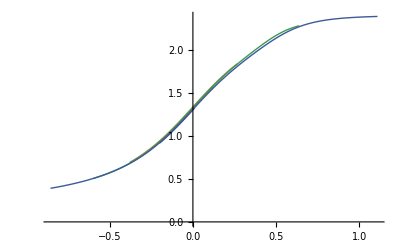

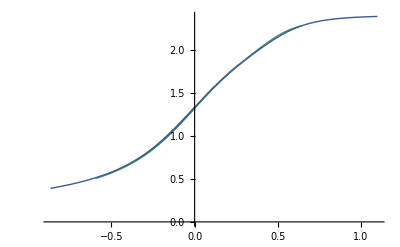

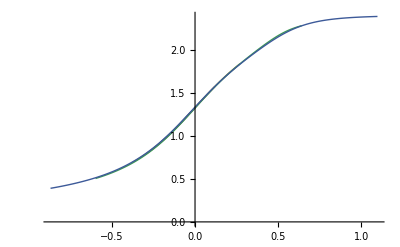

```mathematica
b0=1/ν;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

absMs1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs3[l]=Table[{(absM[l][[All,1]][[i]]-(k03+c03*l^(ex03)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

,{l,{16,24,32,48,64}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True]
ListPlot[{absMs3[16],absMs3[24],absMs3[32],absMs3[48],absMs3[64]},Joined->True]
```

```mathematica
l1=24;
l2=64;

Do[
input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input3[l]=Table[{(absM[l][[All,1]][[i]]-(k03+c03*l^(ex03))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=1.5,z<1.7,z+=0.005,
ClearAll[i];

Do[
dat[l]=Table[{input1[l][[All,1]][[i]]*(l)^z,input1[l][[All,2]][[i]]},{i,1,Length[input1[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0115884

1.64 = zf

```mathematica
(*Average Velocity*)
```

```mathematica
v=9;
Logmaxdvdd[v]
Logvvpmaxdvdd[v]
pmaxdvdd[v]
```

```mathematica
Logmaxdvdd[v]={{Log[5000],5.358169631350033},{Log[10000],5.167567815298064},{Log[20000],4.961401281440647},{Log[30000],4.857775447451913},{Log[50000],4.774807469779157}};
```

```mathematica
Logvvpmaxdvdd[v]={{Log[5000],2.1473556335766033},{Log[10000],2.156363230189808},{Log[20000],2.158432927677586},{Log[30000],2.1625261565205056},{Log[50000],2.16397453751852}};
```

```mathematica
pmaxdvdd[v]={{5000,0.0853},{10000,0.08410000000000001},{20000,0.0835},{30000,0.08310000000000001},{50000,0.0829}};
```

```mathematica
ν=1/0.09;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[Logvvpmaxdvdd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdvdd[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdvdd[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdvdd[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.09

0.08122+c0 x^-ex0

{2.0896+0.00698666 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 2.0896 | 0.0104778 | 199.43 | 2.78009×10^-7
b0 | -0.00698666 | 0.00107074 | -6.52511 | 0.00731399}

{0.08378-442.061/x^55.2964, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.08378 | 0.000610574 | 137.215 | 0.0000531081
c0 | -442.061 | 0. | -∞ | 0.
ex0 | 55.2964 | 0. | ∞ | 0.}

{0.0722858+0.027573/x^0.09, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0722858 | 0.00135178 | 53.4745 | 0.000014404
c0 | 0.027573 | 0.00323399 | 8.52601 | 0.00338948}

{0.08122+0.130032/x^0.408622, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.408622 | 0.0252883 | 16.1586 | 0.000515593
c0 | 0.130032 | 0.030431 | 4.273 | 0.0235312}

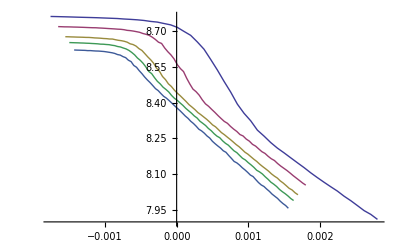

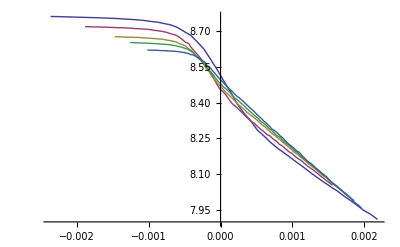

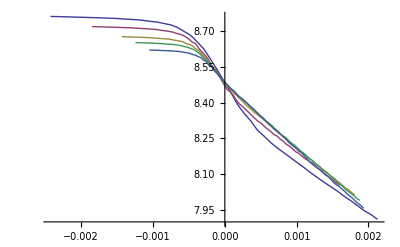

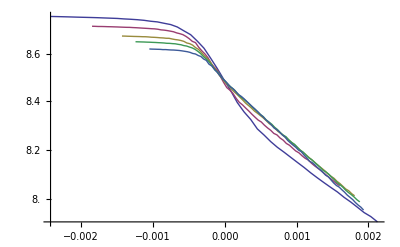

```mathematica
b0=-0.09;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

vels1[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];

vels2[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];

vels3[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{vels1[v][5],vels1[v][10],vels1[v][20],vels1[v][30],vels1[v][50]},Joined->True]
ListPlot[{vels2[v][5],vels2[v][10],vels2[v][20],vels2[v][30],vels2[v][50]},Joined->True]
ListPlot[{vels3[v][5],vels3[v][10],vels3[v][20],vels3[v][30],vels3[v][50]},Joined->True]
ListLogPlot[{vels3[v][5],vels3[v][10],vels3[v][20],vels3[v][30],vels3[v][50]},Joined->True]
```

```mathematica
l1=10;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(vel[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0296144

-0.12 = zf

```mathematica
(*Gap*)
```

```mathematica
v=9;
Logmaxdgdd[v]
Logvvpmaxdgdd[v]
pmaxdgdd[v]
```

```mathematica
Logmaxdgdd[v]={{Log[5000],3.0811151263243617},{Log[10000],2.9015238553373988},{Log[20000],2.7106688527724607},{Log[30000],2.610442884899177},{Log[50000],2.523909941470408}};
```

```mathematica
Logvvpmaxdgdd[v]={{Log[5000],-3.592897068472406},{Log[10000],-3.8752634916196365},{Log[20000],-3.930004202535882},{Log[30000],-3.9727304744263137},{Log[50000],-4.196067701162642}};
```

```mathematica
pmaxdgdd[v]={{5000,0.0853},{10000,0.08410000000000001},{20000,0.0835},{30000,0.0833},{50000,0.0829}};
```

```mathematica
ν=1/0.13;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[Logvgpmaxdgdd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdgdd[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdgdd[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdgdd[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.13

0.08122+c0 x^-ex0

{-1.70367-0.226382 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -1.70367 | 0.312288 | -5.45545 | 0.00548669
b0 | 0.226382 | 0.0314635 | 7.19506 | 0.00197724}

{0.08382-442.003/x^58.4948, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.08382 | 0.000590593 | 141.925 | 0.0000496419
c0 | -442.003 | 0. | -∞ | 0.
ex0 | 58.4948 | 0. | ∞ | 0.}

{0.0761314+0.0271638/x^0.13, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0761314 | 0.000858723 | 88.6565 | 3.1633×10^-6
c0 | 0.0271638 | 0.00301676 | 9.0043 | 0.00289178}

{0.08122+0.10913/x^0.388496, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.388496 | 0.0274275 | 14.1645 | 0.000762307
c0 | 0.10913 | 0.0277715 | 3.92957 | 0.0293385}

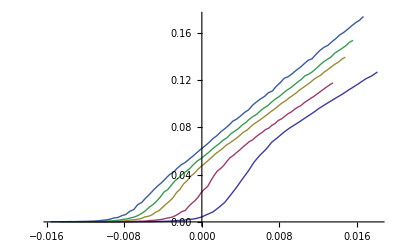

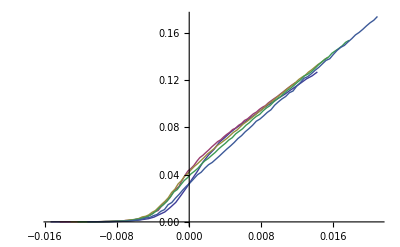

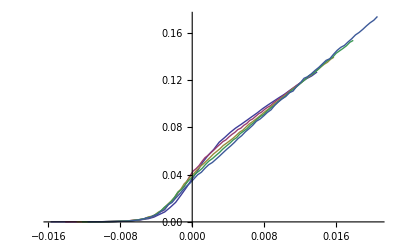

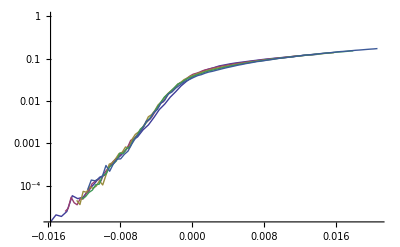

```mathematica
b0=0.13;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

gaps1[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,gap[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[gap[v][l]]}];

gaps2[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,gap[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[gap[v][l]]}];

gaps3[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,gap[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[gap[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{gaps1[v][5],gaps1[v][10],gaps1[v][20],gaps1[v][30],gaps1[v][50]},Joined->True]
ListPlot[{gaps2[v][5],gaps2[v][10],gaps2[v][20],gaps2[v][30],gaps2[v][50]},Joined->True]
ListPlot[{gaps3[v][5],gaps3[v][10],gaps3[v][20],gaps3[v][30],gaps3[v][50]},Joined->True]
ListLogPlot[{gaps3[v][5],gaps3[v][10],gaps3[v][20],gaps3[v][30],gaps3[v][50]},Joined->True]
```

```mathematica
l1=20;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(gap[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),gap[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[gap[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.00210405

0.13 = zf

```mathematica
(*Vel*)
```

```mathematica
(*Initiation: *)
```

```mathematica
v=9;
ive[v][5]=Interpolation[vel5v9];
ive[v][10]=Interpolation[vel10v9];
ive[v][20]=Interpolation[vel20v9];
ive[v][30]=Interpolation[vel30v9];
ive[v][40]=Interpolation[vel40v9];
ive[v][50]=Interpolation[vel50v9];
```

```mathematica
v=9;
ve[v][5]= vel5v9;
ve[v][10]= vel10v9;
ve[v][20]= vel20v9;
ve[v][30]= vel30v9;
ve[v][40]= vel40v9;
ve[v][50]= vel50v9;
```

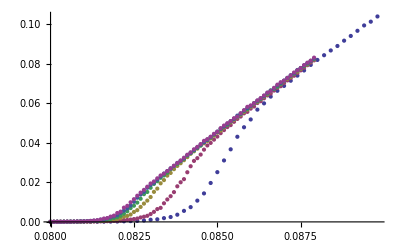

```mathematica
ListPlot[{vel5v9,vel10v9,vel20v9,vel30v9,vel40v9,vel50v9}]
```

```mathematica
δ=0.0008;
v=9;
Do[
dvedd[v][l]=Table[{x,(ive[v][l][x+δ]-ive[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0002}];
,{l,{5,10,20,30,40,50}}]
```

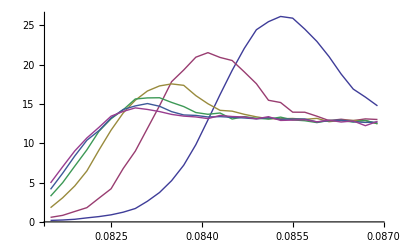

```mathematica
ListLinePlot[{dvedd[v][5],dvedd[v][10],dvedd[v][20],dvedd[v][30],dvedd[v][40],dvedd[v][50]}]
```

```mathematica
maxdvedd[v]=Table[{l*1000,Max[dvedd[v][l][[All,2]]]},{l,{5,10,20,30,40,50}}]
Logmaxdvedd[v]=Table[{Log[maxdvedd[v][[All,1]][[i]]],Log[maxdvedd[v][[All,2]][[i]]]},{i,1,Length[maxdvedd[v]]}]

pmaxdvedd[v]=Table[{maxdvedd[v][[All,1]][[i]],Select[dvedd[v][maxdvedd[v][[All,1]][[i]]/1000],#[[2]]==maxdvedd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdvedd[v]]}]


vvpmaxdvedd[v]=Table[{pmaxdvedd[v][[All,1]][[i]],Select[ve[v][pmaxdvedd[v][[All,1]][[i]]/1000],#[[1]]==pmaxdvedd[v][[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[pmaxdvedd[v]]}]

vvpmaxdvedd[v]={{5000,0.033825213125},{10000,0.02507711},{20000,0.02338075},{30000,0.022270459999999995},{40000,0.019740129999999998},{50000,0.017782430000000002}}



Logvvpmaxdvedd[v]=Table[{Log[vvpmaxdvedd[v][[All,1]][[i]]],Log[vvpmaxdvedd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdvedd[v]]}]
```

{{5000,26.1494},{10000,21.5425},{20000,17.5633},{30000,15.8033},{40000,15.0635},{50000,14.5124}}

{{Log[5000],3.26383},{Log[10000],3.07003},{Log[20000],2.86581},{Log[30000],2.76022},{Log[40000],2.71228},{Log[50000],2.675}}

{{5000,0.0853},{10000,0.0841},{20000,0.0835},{30000,0.0833},{40000,0.0831},{50000,0.0829}}

{{5000,{}⟦1⟧},{10000,0.0250771},{20000,0.0233808},{30000,0.0222705},{40000,0.0197401},{50000,0.0177824}}

{{5000,0.0338252},{10000,0.0250771},{20000,0.0233808},{30000,0.0222705},{40000,0.0197401},{50000,0.0177824}}

{{Log[5000],-3.38655},{Log[10000],-3.6858},{Log[20000],-3.75584},{Log[30000],-3.80449},{Log[40000],-3.9251},{Log[50000],-4.02954}}

```mathematica
ive[9][5][0.0853]
```

0.0338252

```mathematica
------------------------------------------------------------------------------------------
```

```mathematica
v=9;
Logmaxdvedd[v]
Logvvpmaxdvedd[v]
pmaxdvedd[v]
```

```mathematica
Logmaxdvedd[v]={{Log[5000],3.2638262755734315},{Log[10000],3.070027060845957},{Log[20000],2.865812849908593},{Log[30000],2.7602185812405144},{Log[50000],2.6750047053198958}};
```

```mathematica
Logvvpmaxdvedd[v]={{Log[5000],-3.386548804132127},{Log[10000],-3.685799801117017},{Log[20000],-3.755842244752982},{Log[30000],-3.804494142335704},{Log[50000],-4.029544387818731}};
```

```mathematica
pmaxdvedd[v]={{5000,0.0853},{10000,0.08410000000000001},{20000,0.0835},{30000,0.0833},{50000,0.0829}};
```

```mathematica
ν=1/0.09;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[Logvvpmaxdvedd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdvedd[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdvedd[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdvedd[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.09

0.08122+c0 x^-ex0

{-1.32281-0.247092 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -1.32281 | 0.37973 | -3.48356 | 0.0399522
b0 | 0.247092 | 0.0388048 | 6.36758 | 0.00783921}

{0.08382-442.003/x^58.4948, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.08382 | 0.000590593 | 141.925 | 0.0000496419
c0 | -442.003 | 0. | -∞ | 0.
ex0 | 58.4948 | 0. | ∞ | 0.}

{0.0727055+0.0266623/x^0.09, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0727055 | 0.00131749 | 55.1846 | 0.000013107
c0 | 0.0266623 | 0.00315196 | 8.45895 | 0.0034681}

{0.08122+0.10913/x^0.388496, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.388496 | 0.0274275 | 14.1645 | 0.000762307
c0 | 0.10913 | 0.0277715 | 3.92957 | 0.0293385}

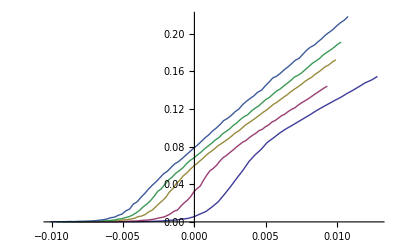

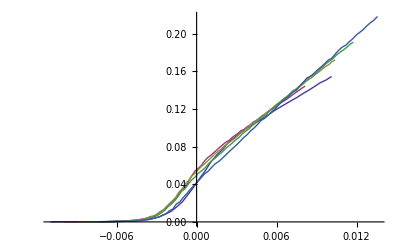

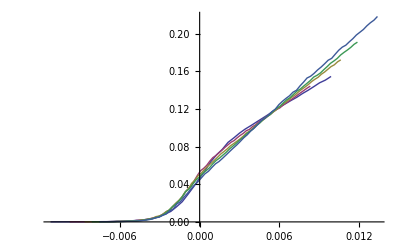

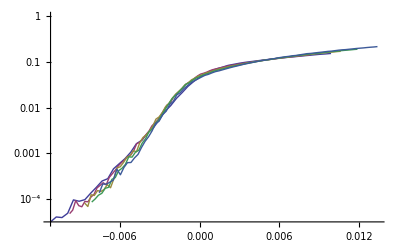

```mathematica
b0=0.09;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

ves1[v][l]=Table[{(ve[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];

ves2[v][l]=Table[{(ve[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];

ves3[v][l]=Table[{(ve[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{ves1[v][5],ves1[v][10],ves1[v][20],ves1[v][30],ves1[v][50]},Joined->True]
ListPlot[{ves2[v][5],ves2[v][10],ves2[v][20],ves2[v][30],ves2[v][50]},Joined->True]
ListPlot[{ves3[v][5],ves3[v][10],ves3[v][20],ves3[v][30],ves3[v][50]},Joined->True]
ListLogPlot[{ves3[v][5],ves3[v][10],ves3[v][20],ves3[v][30],ves3[v][50]},Joined->True]
```

```mathematica
l1=10;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(ve[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0032912

0.13 = zf

```mathematica
(*Chi4*)
```

```mathematica
(*Initiation: *)
```

```mathematica
v=9;
Do[
ichi[v][l]=Interpolation[Chi[v][l]];
,{l,{4,5,8,10,20,30,40,50,100,150,200}}]
```

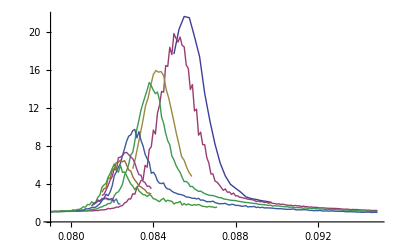

```mathematica
ListLinePlot[{Chi[v][4],Chi[v][5],Chi[v][8],Chi[v][10],Chi[v][20],Chi[v][30],Chi[v][40],Chi[v][50],Chi[v][150],Chi[v][200]},PlotRange->Full]
```

```mathematica
maxChi[v]=Table[{l*1000,Max[Chi[v][l][[All,2]]]},{l,{5,10,20,30,40,50}}]
LogmaxChi[v]=Table[{Log[maxChi[v][[All,1]][[i]]],Log[maxChi[v][[All,2]][[i]]]},{i,1,Length[maxChi[v]]}]

pmaxChi[v]=Table[{maxChi[v][[All,1]][[i]],Select[Chi[v][maxChi[v][[All,1]][[i]]/1000],#[[2]]==maxChi[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxChi[v]]}]
```

{{5000,19.8527},{10000,14.6984},{20000,9.74574},{30000,7.3273},{40000,6.51051},{50000,6.11417}}

{{Log[5000],2.98834},{Log[10000],2.68774},{Log[20000],2.27683},{Log[30000],1.99161},{Log[40000],1.87342},{Log[50000],1.81061}}

{{5000,0.085},{10000,0.0838},{20000,0.0831},{30000,0.0827},{40000,0.0824},{50000,0.0821}}

```mathematica
ν=1/0.09;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[LogmaxChi[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxChi[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxChi[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxChi[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.09

0.08122+c0 x^-ex0

{7.60217-0.538855 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 7.60217 | 0.225342 | 33.7362 | 4.60498×10^-6
b0 | 0.538855 | 0.0227035 | 23.7344 | 0.0000186859}

{0.0831833-470.944/x^59.1881, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0831833 | 0.000563143 | 147.713 | 6.84141×10^-7
c0 | -470.944 | 0. | -∞ | 0.
ex0 | 59.1881 | 0. | ∞ | 0.}

{0.0700307+0.0319543/x^0.09, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0700307 | 0.000637705 | 109.817 | 4.1232×10^-8
c0 | 0.0319543 | 0.00154511 | 20.681 | 0.0000322942}

{0.08122+0.434406/x^0.556265, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.556265 | 0.0283394 | 19.6286 | 0.0000397295
c0 | 0.434406 | 0.11294 | 3.84636 | 0.0183595}

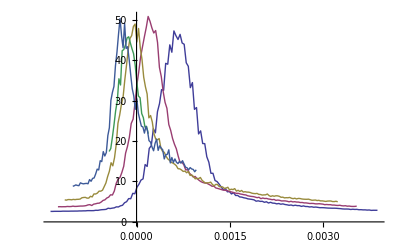

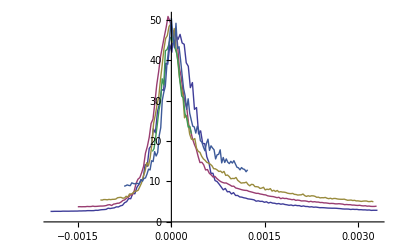

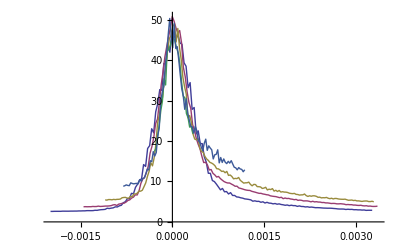

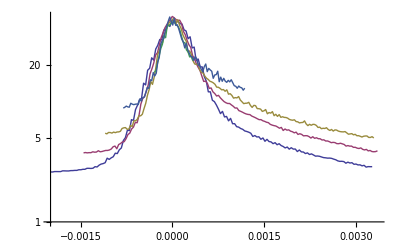

```mathematica
b0=-0.13;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

Chis1[v][l]=Table[{(Chi[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];

Chis2[v][l]=Table[{(Chi[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];

Chis3[v][l]=Table[{(Chi[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{Chis1[v][5],Chis1[v][10],Chis1[v][20],Chis1[v][30],Chis1[v][50]},Joined->True]
ListPlot[{Chis2[v][5],Chis2[v][10],Chis2[v][20],Chis2[v][30],Chis2[v][50]},Joined->True]
ListPlot[{Chis3[v][5],Chis3[v][10],Chis3[v][20],Chis3[v][30],Chis3[v][50]},Joined->True]
ListLogPlot[{Chis3[v][5],Chis3[v][10],Chis3[v][20],Chis3[v][30],Chis3[v][50]},Joined->True]
```

```mathematica
l1=10;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(Chi[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

3.96656

-0.13 = zf